Attempt to find likelihood of DM model

Note: input mass of dark matter in GeV

#### Make spectral file of model

Define dN/dE for b-bbar that gets the flux of photons given the mass of dark matter (mdm) and ratio x (where x = E/mdm).

```mathematica
Get["/Users/austingottfredson/Documents/Macbook/School/20 Fall/Dark Matter/dlNdlxEW.m"];
```

```mathematica
dnde[mdm_,x_]:=10^(dlNdlxIEW["b"->"γ"][mdm,Log[10,x]])/(Log[10]);
```

Use specfile if you want a spectrum plot for a given mass of DM.

```mathematica
specfile[mdm_]:=With[{i:=10^xp},Table[{i*mdm,dnde[mdm,i]},{xp,-7,0,.2}]];
```

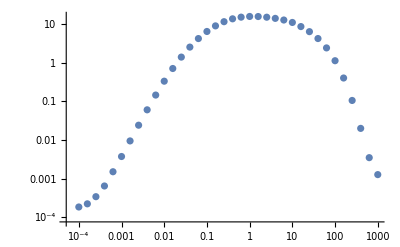

```mathematica
ListLogLogPlot[specfile[1000]]
```

#### Predict normalized energy of model for one energy bin

Import likelihood file and separate the columns

```mathematica
likefile="http://www-glast.stanford.edu/pub_data/1048/like_draco.txt";
data=Import[likefile,"Table"];
data2=Drop[data,2];
emins=Flatten[DeleteDuplicates[data2[[All,1]]]];
emaxs=Flatten[DeleteDuplicates[data2[[All,2]]]];
efluxeslikes=data2[[All,{1,3,4}]];
loglikes=Flatten[data2[[All,4]]];
```

Integrate a generic spectrum, multiplied by E, to get the energy flux. Divide by 1000 to change from GeV to MeV. The units will just be MeV for an energy bin with a given emin and emax. This is normalized per sing dark matter annihilation.

```mathematica
pred[mdm_,ebin_]:=NIntegrate[dnde[mdm,energy/mdm],{energy,emins[[ebin]],emaxs[[ebin]]}]/1000;
```

#### Eq. 1 from Fermi analysis for one energy bin

Define J factor

```mathematica
jfactor=10^18.8;
```

eflux in MeV/cm^2/s

```mathematica
eflux[sigmav_,mdm_,ebin_]:=sigmav/(8*Pi*(mdm^2))*pred[mdm,ebin]*jfactor
```

#### Plot for sigmav vs eflux

```mathematica
efluxplot=With[{i:=10^xp},Table[{i,eflux[i,1000,1]},{xp,-30,-20,1}]];
```

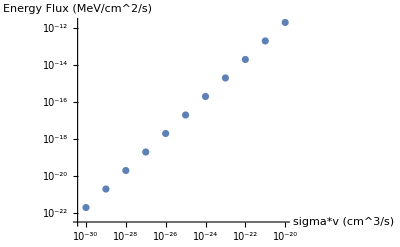

```mathematica
ListLogLogPlot[efluxplot,AxesLabel->{"sigma*v (cm^3/s)","Energy Flux (MeV/cm^2/s)"}]
```

#### Plot for sigmav vs likelihood

Make a loop to separate efluxeslikes into each bin and then train interpolation.
1) separate efluxeslikes into bins
2) train interpolation for each energy bin
3) input eflux into interpolation to get deltaloglike for each energy bin
4) add deltaloglike of each energy bin together

```mathematica
likebin[bin_]:=Select[efluxeslikes,#[[1]]==emins[[bin]]&][[All,{2,3}]];
```

Train interpolation of likelihood file for each bin.

```mathematica
likeinterp[sigmav_,mdm_,bin_]:=Interpolation[likebin[bin],eflux[sigmav,mdm,bin]];
```

Find the likelihood given eflux found from the eflux function

```mathematica
likeinterp[10^-24,1000,11]
```

InterpolatingFunction::dmval: Input value {0.000214912} lies outside the range of data in the interpolating function. Extrapolation will be used.

-6662.65

```mathematica
emins[[11]]
```

8891.4

```mathematica
eflux[10^-24,1000,11]
```

0.000214912